```mathematica
(*Зададим данную функцию и построим ее график*)f[x_,y_]=3*x^2*y+y^3-12*x-15*y+3;
Plot3D[f[x,y],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
(*Локализуем точку максимума функции*)
G=Plot3D[f[x,y],{x,-2,1},{y,-4,-1}]
```

-Graphics3D-

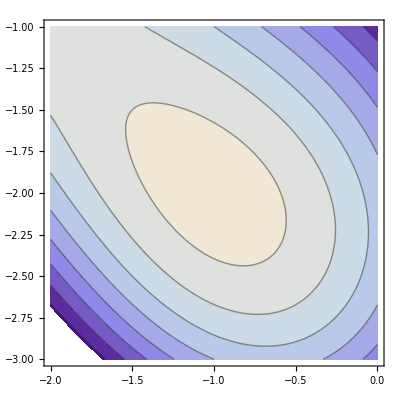

```mathematica
(*Построим линии уровня в окрестности точки максимума*)
GC=ContourPlot[f[x,y],{x,-2,0},{y,-3,-1}]
```

```mathematica
(*Зададим точность вычислений*)
eps=10^(-5);
(*Найдем градиент данной функции*)n[x_,y_]=Grad[f[x,y],{x,y}]/Norm[Grad[f[x,y],{x,y}]];
(*Зададим начальное приближение к точке максимума*)
M0={0,-1};
(*Зададим длину шага приближения к точке экстремума*)
lambda=1;
(*Зададим счетчик количества итераций*)
k=0;
IT={M0};
(*Реализуем алгоритм градиентного метода поиска экстремума*)
While[lambda≥eps,
M1=M0+lambda*N[n[M0[[1]],M0[[2]]]];If[f[M1[[1]],M1[[2]]]>f[M0[[1]],M0[[2]]],M0=M1;M1=M0+lambda*N[n[M0[[1]],M0[[2]]]];k=k+1;AppendTo[IT,M1],
lambda=lambda/2;M1=M0+lambda*N[n[M0[[1]],M0[[2]]]]]
]
Print["Точка максимума равна: ",N[M1]]
Print["Количество итераций равно: ",k];
```

Точка максимума равна: {-0.999996,-2.}

Количество итераций равно: 10

```mathematica
IT3D=Table[{IT[[i]][[1]],IT[[i]][[2]],f[IT[[i]][[1]],IT[[i]][[2]]]},{i,1,k+1}];
GIT3D=ListPointPlot3D[IT3D,PlotStyle->Red];
Show[G,GIT3D]
```

-Graphics3D-

```mathematica
Animate[Show[G,ListPointPlot3D[{IT3D[[i]]},PlotStyle->Red]],{i,1,k+1,1},AnimationRunning->False]
```

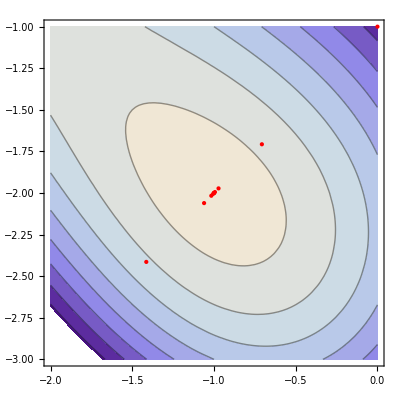

```mathematica
GIT=ListPlot[IT,PlotStyle->Red];
Show[GC,GIT]
```

```mathematica
Animate[Show[GC,ListPlot[{IT[[i]]},PlotStyle->Red]],{i,1,k+1,1},AnimationRunning->False]
```